# Moments of the lattice An

## The G recursion

```mathematica
Clear[G];
G[n_,0,0]:=1;
G[1,k_,m_]:=
1/(2*k +m+1);
G[n_,k_,m_]:=G[n,k,m]=Sum[Sum[Binomial[k,j]*Binomial[m,jd]*1/(2*j +jd+1)*G[n-1,k-j,m-jd],{jd,0,m}],{j,0,k}];
```

```mathematica
G[3,2,2]
```

1235/252

## The moment coefficient

```mathematica
Clear[Mc];
Mc[n_,m_]:=Mc[n,m]=Sum[Sum[Sum[Binomial[m,k]*(1-1/(n+1))^k*Multinomial[j1,j2,m-k-j1-j2]*(-1/(n+1))^(m-k-j1)*2^j2*G[n-1,j1,j2+2*(m-k-j1-j2)],{j2,0,m-k-j1}],{j1,0,m-k}],{k,0,m}];
```

```mathematica
Mc[5,3]/Factorial[3]
```

1/6 Mc[5,3]

```mathematica
Mc[2,2]
```

14/45

## The moment

```mathematica
eucpower[n_,m_]:=n*Sqrt[n+1]*Mc[n,m]/(n+2*m);
```

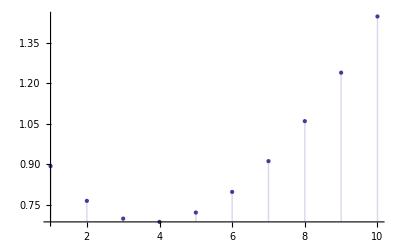

{0.0346478,0.0945982,0.212717,0.419295,0.752256,1.25762,1.98999,3.01298,4.39965}

```mathematica
DiscretePlot[Log[eucpower[8,m]], {m,1,10}]
Table[N[eucpower[n,4]],{n,2,10}]
```

## The probability of error

```mathematica
Pe[n_,v_,t_] :=1 - Sum[(-1)^m/2^m/v^m/Factorial[m]*eucpower[n,m],{m,0,t}]/(2*Pi*v)^(n/2);
N[Pe[2,10/100,33]]
```

0.0652598

## Plotting the probability of error versus SNR

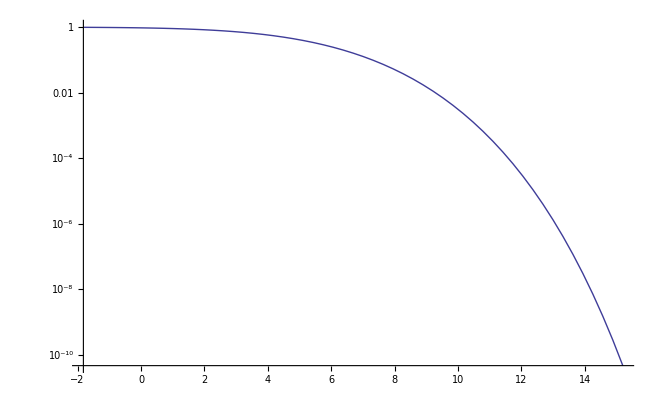

```mathematica
n = 8;
V = Sqrt[n+1];
vars = Table[1/2*(93/100)^k, {k,0,54}];
snrdb = 10*Log10[V^(2/n)/(4#)] &/@ vars;
pes = Pe[n,#,320]&/@ vars;
ListLogPlot[Thread[{ snrdb,pes }],Joined->{True}]
```

Execute below to write the result to a file suitable for making a metapost plot.

```mathematica
ToMetaPostString[v_] := ToString[NumberForm[v,ExponentFunction->(1 Quotient[#,1]&),NumberFormat->(Row[{#1,"e",#3}]&)]]
fname = FileNameJoin[{Directory[],"/Software/An_lattice_error_probability/plots/pe" <> ToString[n]}]
str = OpenWrite[fname]
Do[WriteString[str, ToMetaPostString[N[snrdb[[k]]]] <> "\t"  <> ToMetaPostString[N[pes[[k]]]]  "\n"],{k,Length[pes]}]
Close[str]
FilePrint[%]
```

/home/mckillrg/Software/An_lattice_error_probability/plots/pe8

OutputStream[/home/mckillrg/Software/An_lattice_error_probability/plots/pe8,54]

/home/mckillrg/Software/An_lattice_error_probability/plots/pe8

-1.8175e0	9.86002e-1
 -1.50233e0	9.82328e-1
 -1.18716e0	9.77779e-1
 -8.71985e-1	9.72177e-1
 -5.56815e-1	9.65318e-1
 -2.41644e-1	9.56975e-1
 7.35263e-2	9.46892e-1
 3.88697e-1	9.34796e-1
 7.03867e-1	9.20393e-1
 1.01904e0	9.03386e-1
 1.33421e0	8.83476e-1
 1.64938e0	8.60383e-1
 1.96455e0	8.33861e-1
 2.27972e0	8.03719e-1
 2.59489e0	7.69844e-1
 2.91006e0	7.3222e-1
 3.22523e0	6.90956e-1
 3.5404e0	6.46299e-1
 3.85557e0	5.98649e-1
 4.17074e0	5.4856e-1
 4.48591e0	4.96736e-1
 4.80108e0	4.44008e-1
 5.11625e0	3.91301e-1
 5.43143e0	3.39593e-1
 5.7466e0	2.89856e-1
 6.06177e0	2.43002e-1
 6.37694e0	1.99823e-1
 6.69211e0	1.60941e-1
 7.00728e0	1.26774e-1
 7.32245e0	9.75113e-2
 7.63762e0	7.31205e-2
 7.95279e0	5.33629e-2
 8.26796e0	3.78336e-2
 8.58313e0	2.60095e-2
 8.8983e0	1.73035e-2
 9.21347e0	1.11164e-2
 9.52864e0	6.88088e-3
 9.84381e0	4.09391e-3
 1.0159e1	2.33527e-3
 1.04742e1	1.27368e-3
 1.07893e1	6.62269e-4
 1.11045e1	3.27269e-4
 1.14197e1	1.53183e-4
 1.17348e1	6.76673e-5
 1.205e1	2.81004e-5
 1.23652e1	1.0924e-5
 1.26803e1	3.95733e-6
 1.29955e1	1.32933e-6
 1.33107e1	4.11855e-7
 1.36259e1	1.1701e-7
 1.3941e1	3.02933e-8
 1.42562e1	7.09839e-9
 1.45714e1	1.49444e-9
 1.48865e1	2.80449e-10
 1.52017e1	4.65126e-11
 1.55169e1	-1.2419e-9